0.001

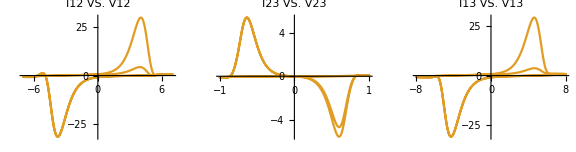

```mathematica
Clear[n0,f1,β,kb,tmax,omega,vamp,E01,E02,T,Ron,Roff,nboundary,kar1,kar2,a,b,CC1,CC2,EE,alfa,Ra,VZ,RR,ZZ,V,V0,kox,kre,kox0,kred0,phase,V2,Sida]

kox0=0.08; (*原本是0.008*)
kred0=0.00001;(*原本是0.0001*)
CC3=(2*10^-9);
 (*CC3=(2*10^-9);*)
CC2=1*CC3;
ff=1*10^6;
Ron=5*10^9;
Roff=Ron*1.2;
n01=10*10^5;
n02=1*10^5;
n03=1*10^5;
alfa1=30; (*40*)
freq=0.01; (*0.08*)
freq2=0.001

kb=8.615*10^(-5);
Eox=3.5;
Ere=3.8;
T=300;
EE=(1.6*10^-19);

(*-------------------------------------- V --------------------------------------*)
V1[t_]:=8*Sin[2*Pi*t*freq];
V2[t_]:=1*Sin[2*Pi*t*freq];
V3[t_]:=0;
V12[t_]:=V1[t]-V2[t];
V13[t_]:=V1[t]-V3[t];
V23[t_]:=V2[t]-V3[t];

 


(*PLOTTING THE SOURCE VOLTAGE*)
(*plotmp=ParametricPlot[{t,V12[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V12"]
plotmp=ParametricPlot[{t,V23[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V23"]
plotmp=ParametricPlot[{t,V13[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V13"]*)
(*V[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq])-(Sin[t*2*Pi*freq*3])/9+(Sin[t*2*Pi*freq*5])/25)
V1[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq+Pi/5])-(Sin[t*2*Pi*freq*3+Pi/5])/9+(Sin[t*2*Pi*freq*5+Pi/5])/25)*)


(*-------------------------------------- kox & kre --------------------------------------*)

kox12[t_]:=kox0*Exp[-(Eox-(V12[t]))/(alfa1*kb*T)];
kox13[t_]:=kox0*Exp[-(Eox-(V13[t]))/(alfa1*kb*T)];
kre12[t_]:=kred0*Exp[(Ere-(V12[t]))/(alfa1*kb*T)];
kre13[t_]:=kred0*Exp[(Ere-(V13[t]))/(alfa1*kb*T)];
kox23[t_]:=kox0*Exp[-(Eox-(V23[t]))/(alfa1*kb*T)];
kre23[t_]:=kred0*Exp[(Ere-(V23[t]))/(alfa1*kb*T)];
kox21[t_]:=kox0*Exp[-(Eox+(V12[t]))/(alfa1*kb*T)];
kre21[t_]:=kred0*Exp[(Ere+(V12[t]))/(alfa1*kb*T)];
kox31[t_]:=kox0*Exp[-(Eox+(V13[t]))/(alfa1*kb*T)];
kre31[t_]:=kred0*Exp[(Ere+(V13[t]))/(alfa1*kb*T)];
kox32[t_]:=kox0*Exp[-(Eox+(V23[t]))/(alfa1*kb*T)];
kre32[t_]:=kred0*Exp[(Ere+(V23[t]))/(alfa1*kb*T)];
(*-------------------------------------- Equation --------------------------------------*)

s=NDSolve[{nd1'[t]/n01==(kox12[t]*(1-nd1[t]/n01)-kre12[t]*nd1[t]/n01)+(kox13[t]*(1-nd1[t]/n01)-kre13[t]*nd1[t]/n01),nd1[0]/n01==0.828,nd2'[t]/n02==(kox23[t]*(1-nd2[t]/n02)-kre23[t]*nd2[t]/n02)+(kox21[t]*(1-nd2[t]/n02)-kre21[t]*nd2[t]/n02),nd2[0]/n02==0.828,
nd3'[t]/n03==(kox31[t]*(1-nd3[t]/n03)-kre31[t]*nd3[t]/n03)+(kox32[t]*(1-nd3[t]/n03)-kre32[t]*nd3[t]/n03),nd3[0]/n03==0.828
},{nd1,nd2,nd3},{t,0,8000},MaxSteps->Infinity];

(*R[t_]=Evaluate[(Roff/Abs[(nd[t]/n0-0.32)]+Roff/Abs[nd[t]/n0-0.32])/.s];*)
R1[t_]:=Evaluate[((1-nd1[t]/n01)*Roff+nd1[t]/n01*Ron)/.s];
C1[t_]:=Evaluate[(1/(1/CC2+nd1[t]/n01*(1/CC3-1/CC2)))/.s];
R2[t_]:=Evaluate[((1-nd2[t]/n02)*Roff+nd2[t]/n02*Ron)/.s];
C2[t_]:=Evaluate[(1/(1/CC2+nd2[t]/n02*(1/CC3-1/CC2)))/.s];
R3[t_]:=Evaluate[((1-nd3[t]/n03)*Roff+nd3[t]/n03*Ron)/.s];
C3[t_]:=Evaluate[(1/(1/CC2+nd3[t]/n03*(1/CC3-1/CC2)))/.s];

R12[t]=R1[t]+R2[t];
R23[t]=R2[t]+R3[t];
R13[t]=R1[t]+R3[t];
CC12[t]=(1/C1[t]+1/C2[t])^(-1);
CC13[t]=(1/C1[t]+1/C3[t])^(-1);
CC23[t]=(1/C2[t]+1/C3[t])^(-1);

(*CC[t_]=CC3*)

(*I12 VS V*)
plotmp1=ParametricPlot[{V12[t],Evaluate[(ff*EE*(nd1'[t]+nd2'[t])+((V12[t]/R12[t])+(D[CC12[t]*V12[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I12 VS. V12"];
plotmp2=ParametricPlot[{V23[t],Evaluate[(ff*EE*(nd2'[t]+nd3'[t])+((V23[t]/R23[t])+(D[CC23[t]*V23[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I23 VS. V23"] ;
plotmp3=ParametricPlot[{V13[t],Evaluate[(ff*EE*(nd1'[t]+nd3'[t])+((V13[t]/R13[t])+(D[CC13[t]*V13[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I13 VS. V13"];
 
GraphicsRow[{plotmp1,plotmp2,plotmp3}, PlotLabel->{"test"},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic6.jpg",%6804,"JPEG"]
```

C:\Users\Bailey\Desktop\pic6.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic1.jpg",%6534,"JPEG"]
```

C:\Users\Bailey\Desktop\pic1.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic5.jpg",%6480,"JPEG"]
```

C:\Users\Bailey\Desktop\pic5.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic4.jpg",%6480,"JPEG"]
```

C:\Users\Bailey\Desktop\pic4.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic3.jpg",%5699,"JPEG"]
```

C:\Users\Bailey\Desktop\pic3.jpg

C:\Users\Bailey\Desktop\pic2.jpg

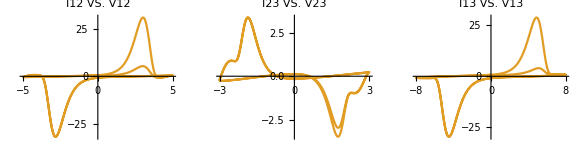

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic2.jpg",%5386,"JPEG"]
```

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic1.jpg",%5281,"JPEG"]
```

C:\Users\Bailey\Desktop\pic1.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\pic1.jpg",%5279,"JPEG"]
```

C:\Users\Bailey\Desktop\pic1.jpg

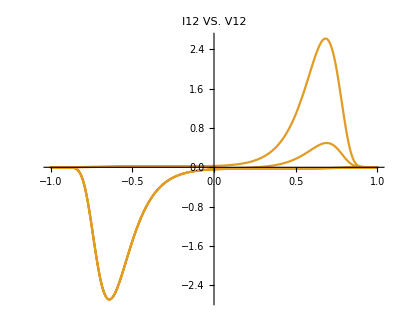

```mathematica
ParametricPlot[{V12[t],Evaluate[(ff*EE*(nd2'[t]))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I12 VS. V12"]
```

```mathematica
(* Here I include the diffusive current term and to see the differences *)
```

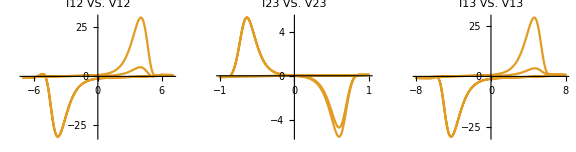

```mathematica
Clear[n0,f1,β,kb,tmax,omega,vamp,E01,E02,T,Ron,Roff,nboundary,kar1,kar2,a,b,CC1,CC2,EE,alfa,Ra,VZ,RR,ZZ,V,V0,kox,kre,kox0,kred0,phase,V2,Sida]

kox0=0.08; (*原本是0.008*)
kred0=0.00001;(*原本是0.0001*)
CC3=(2*10^-9);
 (*CC3=(2*10^-9);*)
CC2=1*CC3;
ff=1*10^6;
Ron=5*10^9;
Roff=Ron*1.2;
n01=10*10^5;
n02=1*10^5;
n03=1*10^5;
alfa1=30; (*40*)
freq=0.01; (*0.08*)
freq2=0.001;
d12=10^(-9);
d13=10^(-9);
d23=10^(-9);
d31=d13;
d21=d12;
d32=d23;
L=50*10^(-9);

kb=8.615*10^(-5);
Eox=3.5;
Ere=3.8;
T=300;
EE=(1.6*10^-19);

(*-------------------------------------- V --------------------------------------*)
V1[t_]:=8*Sin[2*Pi*t*freq];
V2[t_]:=1*Sin[2*Pi*t*freq];
V3[t_]:=0;
V12[t_]:=V1[t]-V2[t];
V13[t_]:=V1[t]-V3[t];
V23[t_]:=V2[t]-V3[t];

 


(*PLOTTING THE SOURCE VOLTAGE*)
(*plotmp=ParametricPlot[{t,V12[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V12"]
plotmp=ParametricPlot[{t,V23[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V23"]
plotmp=ParametricPlot[{t,V13[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V13"]*)
(*V[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq])-(Sin[t*2*Pi*freq*3])/9+(Sin[t*2*Pi*freq*5])/25)
V1[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq+Pi/5])-(Sin[t*2*Pi*freq*3+Pi/5])/9+(Sin[t*2*Pi*freq*5+Pi/5])/25)*)


(*-------------------------------------- kox & kre --------------------------------------*)

kox12[t_]:=kox0*Exp[-(Eox-(V12[t]))/(alfa1*kb*T)];
kox13[t_]:=kox0*Exp[-(Eox-(V13[t]))/(alfa1*kb*T)];
kre12[t_]:=kred0*Exp[(Ere-(V12[t]))/(alfa1*kb*T)];
kre13[t_]:=kred0*Exp[(Ere-(V13[t]))/(alfa1*kb*T)];
kox23[t_]:=kox0*Exp[-(Eox-(V23[t]))/(alfa1*kb*T)];
kre23[t_]:=kred0*Exp[(Ere-(V23[t]))/(alfa1*kb*T)];
kox21[t_]:=kox0*Exp[-(Eox+(V12[t]))/(alfa1*kb*T)];
kre21[t_]:=kred0*Exp[(Ere+(V12[t]))/(alfa1*kb*T)];
kox31[t_]:=kox0*Exp[-(Eox+(V13[t]))/(alfa1*kb*T)];
kre31[t_]:=kred0*Exp[(Ere+(V13[t]))/(alfa1*kb*T)];
kox32[t_]:=kox0*Exp[-(Eox+(V23[t]))/(alfa1*kb*T)];
kre32[t_]:=kred0*Exp[(Ere+(V23[t]))/(alfa1*kb*T)];
(*-------------------------------------- Equation --------------------------------------*)

s=NDSolve[{nd1'[t]/n01==(kox12[t]*(1-nd1[t]/n01)-kre12[t]*nd1[t]/n01)+(kox13[t]*(1-nd1[t]/n01)-kre13[t]*nd1[t]/n01)-d12*(nd1[t]-nd2[t])-d13*(nd1[t]-nd3[t]),nd1[0]/n01==0.828,nd2'[t]/n02==(kox23[t]*(1-nd2[t]/n02)-kre23[t]*nd2[t]/n02)+(kox21[t]*(1-nd2[t]/n02)-kre21[t]*nd2[t]/n02)-d21*(nd2[t]-nd1[t])-d23*(nd2[t]-nd3[t]),nd2[0]/n02==0.828,
nd3'[t]/n03==(kox31[t]*(1-nd3[t]/n03)-kre31[t]*nd3[t]/n03)+(kox32[t]*(1-nd3[t]/n03)-kre32[t]*nd3[t]/n03)-d31*(nd3[t]-nd1[t])-d32*(nd3[t]-nd2[t]),nd3[0]/n03==0.828
},{nd1,nd2,nd3},{t,0,8000},MaxSteps->Infinity];

(*R[t_]=Evaluate[(Roff/Abs[(nd[t]/n0-0.32)]+Roff/Abs[nd[t]/n0-0.32])/.s];*)
R1[t_]:=Evaluate[((1-nd1[t]/n01)*Roff+nd1[t]/n01*Ron)/.s];
C1[t_]:=Evaluate[(1/(1/CC2+nd1[t]/n01*(1/CC3-1/CC2)))/.s];
R2[t_]:=Evaluate[((1-nd2[t]/n02)*Roff+nd2[t]/n02*Ron)/.s];
C2[t_]:=Evaluate[(1/(1/CC2+nd2[t]/n02*(1/CC3-1/CC2)))/.s];
R3[t_]:=Evaluate[((1-nd3[t]/n03)*Roff+nd3[t]/n03*Ron)/.s];
C3[t_]:=Evaluate[(1/(1/CC2+nd3[t]/n03*(1/CC3-1/CC2)))/.s];

R12[t]=R1[t]+R2[t];
R23[t]=R2[t]+R3[t];
R13[t]=R1[t]+R3[t];
CC12[t]=(1/C1[t]+1/C2[t])^(-1);
CC13[t]=(1/C1[t]+1/C3[t])^(-1);
CC23[t]=(1/C2[t]+1/C3[t])^(-1);

(*CC[t_]=CC3*)

(*I12 VS V*)
plotmp1=ParametricPlot[{V12[t],Evaluate[(EE*d12*(nd1[t]-nd2[t])/L+ff*EE*(nd1'[t]+nd2'[t])+((V12[t]/R12[t])+(D[CC12[t]*V12[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I12 VS. V12"];
plotmp2=ParametricPlot[{V23[t],Evaluate[(EE*d23*(nd2[t]-nd3[t])/L+ff*EE*(nd2'[t]+nd3'[t])+((V23[t]/R23[t])+(D[CC23[t]*V23[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I23 VS. V23"] ;
plotmp3=ParametricPlot[{V13[t],Evaluate[(EE*d13*(nd1[t]-nd3[t])/L+ff*EE*(nd1'[t]+nd3'[t])+((V13[t]/R13[t])+(D[CC13[t]*V13[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I13 VS. V13"];
 
GraphicsRow[{plotmp1,plotmp2,plotmp3}, PlotLabel->{"test"},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d1.jpg",%296,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d1.jpg

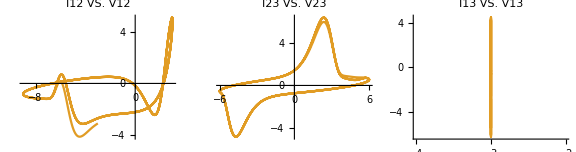

```mathematica
Clear[n0,f1,β,kb,tmax,omega,vamp,E01,E02,T,Ron,Roff,nboundary,kar1,kar2,a,b,CC1,CC2,EE,alfa,Ra,VZ,RR,ZZ,V,V0,kox,kre,kox0,kred0,phase,V2,Sida]

kox0=0.08; (*原本是0.008*)
kred0=0.00001;(*原本是0.0001*)
CC3=(2*10^-9);
 (*CC3=(2*10^-9);*)
CC2=1*CC3;
ff=1*10^6;
Ron=5*10^9;
Roff=Ron*1.2;
n01=10*10^5;
n02=1*10^5;
n03=0.1*10^5;
alfa1=30; (*40*)
freq=0.02; (*0.08*)
freq2=0.001;
d12=1*10^(-9);
d13=1*10^(-9) ;
d23=1*10^(-9);
d31=d13;
d21=d12;
d32=d23;
L=300*10^(-9);

kb=8.615*10^(-5);
Eox=3.5;
Ere=3.8;
T=300;
EE=(1.6*10^-19);

(*-------------------------------------- V --------------------------------------*)
V1[t_]:=-3;
V2[t_]:=6*Sin[2*Pi*t*freq];
V3[t_]:=0;
V12[t_]:=V1[t]-V2[t];
V13[t_]:=V1[t]-V3[t];
V23[t_]:=V2[t]-V3[t];

 


(*PLOTTING THE SOURCE VOLTAGE*)
(*plotmp=ParametricPlot[{t,V12[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V12"]
plotmp=ParametricPlot[{t,V23[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V23"]
plotmp=ParametricPlot[{t,V13[t]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"V13"]*)
(*V[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq])-(Sin[t*2*Pi*freq*3])/9+(Sin[t*2*Pi*freq*5])/25)
V1[t_]=9*8/Pi/Pi*((Sin[t*2*Pi*freq+Pi/5])-(Sin[t*2*Pi*freq*3+Pi/5])/9+(Sin[t*2*Pi*freq*5+Pi/5])/25)*)


(*-------------------------------------- kox & kre --------------------------------------*)

kox12[t_]:=kox0*Exp[-(Eox-(V12[t]))/(alfa1*kb*T)];
kox13[t_]:=kox0*Exp[-(Eox-(V13[t]))/(alfa1*kb*T)];
kre12[t_]:=kred0*Exp[(Ere-(V12[t]))/(alfa1*kb*T)];
kre13[t_]:=kred0*Exp[(Ere-(V13[t]))/(alfa1*kb*T)];
kox23[t_]:=kox0*Exp[-(Eox-(V23[t]))/(alfa1*kb*T)];
kre23[t_]:=kred0*Exp[(Ere-(V23[t]))/(alfa1*kb*T)];
kox21[t_]:=kox0*Exp[-(Eox+(V12[t]))/(alfa1*kb*T)];
kre21[t_]:=kred0*Exp[(Ere+(V12[t]))/(alfa1*kb*T)];
kox31[t_]:=kox0*Exp[-(Eox+(V13[t]))/(alfa1*kb*T)];
kre31[t_]:=kred0*Exp[(Ere+(V13[t]))/(alfa1*kb*T)];
kox32[t_]:=kox0*Exp[-(Eox+(V23[t]))/(alfa1*kb*T)];
kre32[t_]:=kred0*Exp[(Ere+(V23[t]))/(alfa1*kb*T)];
(*-------------------------------------- Equation --------------------------------------*)

s=NDSolve[{nd1'[t]/n01==(kox12[t]*(1-nd1[t]/n01)-kre12[t]*nd1[t]/n01)+(kox13[t]*(1-nd1[t]/n01)-kre13[t]*nd1[t]/n01)-d12*(nd1[t]-nd2[t])-d13*(nd1[t]-nd3[t]),nd1[0]/n01==0.128,nd2'[t]/n02==(kox23[t]*(1-nd2[t]/n02)-kre23[t]*nd2[t]/n02)+(kox21[t]*(1-nd2[t]/n02)-kre21[t]*nd2[t]/n02)-d21*(nd2[t]-nd1[t])-d23*(nd2[t]-nd3[t]),nd2[0]/n02==0.128,
nd3'[t]/n03==(kox31[t]*(1-nd3[t]/n03)-kre31[t]*nd3[t]/n03)+(kox32[t]*(1-nd3[t]/n03)-kre32[t]*nd3[t]/n03)-d31*(nd3[t]-nd1[t])-d32*(nd3[t]-nd2[t]),nd3[0]/n03==0.128
},{nd1,nd2,nd3},{t,0,8000},MaxSteps->Infinity];

(*R[t_]=Evaluate[(Roff/Abs[(nd[t]/n0-0.32)]+Roff/Abs[nd[t]/n0-0.32])/.s];*)
R1[t_]:=Evaluate[((1-nd1[t]/n01)*Roff+nd1[t]/n01*Ron)/.s];
C1[t_]:=Evaluate[(1/(1/CC2+nd1[t]/n01*(1/CC3-1/CC2)))/.s];
R2[t_]:=Evaluate[((1-nd2[t]/n02)*Roff+nd2[t]/n02*Ron)/.s];
C2[t_]:=Evaluate[(1/(1/CC2+nd2[t]/n02*(1/CC3-1/CC2)))/.s];
R3[t_]:=Evaluate[((1-nd3[t]/n03)*Roff+nd3[t]/n03*Ron)/.s];
C3[t_]:=Evaluate[(1/(1/CC2+nd3[t]/n03*(1/CC3-1/CC2)))/.s];

R12[t]=R1[t]+R2[t];
R23[t]=R2[t]+R3[t];
R13[t]=R1[t]+R3[t];
CC12[t]=(1/C1[t]+1/C2[t])^(-1);
CC13[t]=(1/C1[t]+1/C3[t])^(-1);
CC23[t]=(1/C2[t]+1/C3[t])^(-1);

(*CC[t_]=CC3*)

(*I12 VS V*)
plotmp1=ParametricPlot[{V12[t],Evaluate[(EE*d12*(nd1[t]-nd2[t])/L+ff*EE*(nd1'[t]+nd2'[t])+((V12[t]/R12[t])+(D[CC12[t]*V12[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I12 VS. V12"];
plotmp2=ParametricPlot[{V23[t],Evaluate[(EE*d23*(nd2[t]-nd3[t])/L+ff*EE*(nd2'[t]+nd3'[t])+((V23[t]/R23[t])+(D[CC23[t]*V23[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I23 VS. V23"] ;
plotmp3=ParametricPlot[{V13[t],Evaluate[(EE*d13*(nd1[t]-nd3[t])/L+ff*EE*(nd1'[t]+nd3'[t])+((V13[t]/R13[t])+(D[CC13[t]*V13[t],t])))*10^9/.s]},{t,0,200},PlotRange->All,AspectRatio->1/1.2,PlotLabel->"I13 VS. V13"];
 
GraphicsRow[{plotmp1,plotmp2,plotmp3}, PlotLabel->{"test"},ImageSize->Large]
```

```mathematica
1
```

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d05.jpg",%943,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d05.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d40.jpg",%883,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d40.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d20.jpg",%823,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d20.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d10.jpg",%763,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d10.jpg

```mathematica
Export["C:\\Users\\Bailey\\Desktop\\3T_DNA\\diffusion_d5.jpg",%703,"JPEG"]
```

C:\Users\Bailey\Desktop\3T_DNA\diffusion_d5.jpg